```mathematica
conditions={0,0};
```

```mathematica
list=Table[f[i],{i,1,21}];
```

```mathematica
f[1]=a;f[201]=b;
```

```mathematica
Clear[f]
```

```mathematica
list[[1]]
```

a

```mathematica
Take[list,{2,20}]
```

{f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10],f[11],f[12],f[13],f[14],f[15],f[16],f[17],f[18],f[19],f[20]}

```mathematica
Map[MatrixForm,tab=CoefficientArrays[Table[list[[i+1]]-2list[[i]]+list[[i-1]],{i,2,20}],Take[list,{2,20}]]//Normal];
```

```mathematica
a=1;b=1;
```

```mathematica
Inverse[tab[[2]]].tab[[1]]//ListLinePlot
```

-Graphics-

```mathematica
vecs=tab[[2]]//Eigenvectors//N;
```

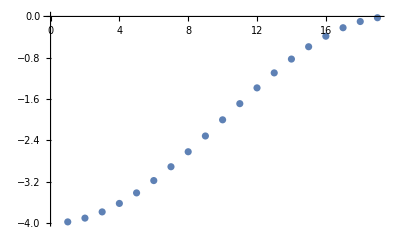

```mathematica
tab[[2]]//Eigenvalues//ListPlot
```

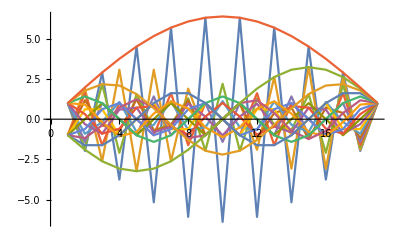

```mathematica
vecs//ListLinePlot
```

```mathematica
Map[MatrixForm,Table[list[[i+1]]-2list[[i]]+list[[i-1]],{i,2,20}]//CoefficientArrays//Normal]
```

{(1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(-2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1)}

```mathematica
list2=Map[#[i+1]-2#[i]+#[i-1]&,list]
```

{f[0][-1+i]-2 f[0][i]+f[0][1+i],f[1][-1+i]-2 f[1][i]+f[1][1+i],f[2][-1+i]-2 f[2][i]+f[2][1+i],f[3][-1+i]-2 f[3][i]+f[3][1+i],f[4][-1+i]-2 f[4][i]+f[4][1+i],f[5][-1+i]-2 f[5][i]+f[5][1+i],f[6][-1+i]-2 f[6][i]+f[6][1+i],f[7][-1+i]-2 f[7][i]+f[7][1+i],f[8][-1+i]-2 f[8][i]+f[8][1+i],f[9][-1+i]-2 f[9][i]+f[9][1+i],f[10][-1+i]-2 f[10][i]+f[10][1+i],f[11][-1+i]-2 f[11][i]+f[11][1+i],f[12][-1+i]-2 f[12][i]+f[12][1+i],f[13][-1+i]-2 f[13][i]+f[13][1+i],f[14][-1+i]-2 f[14][i]+f[14][1+i],f[15][-1+i]-2 f[15][i]+f[15][1+i],f[16][-1+i]-2 f[16][i]+f[16][1+i],f[17][-1+i]-2 f[17][i]+f[17][1+i],f[18][-1+i]-2 f[18][i]+f[18][1+i],f[19][-1+i]-2 f[19][i]+f[19][1+i],f[20][-1+i]-2 f[20][i]+f[20][1+i],f[21][-1+i]-2 f[21][i]+f[21][1+i]}

```mathematica
list2
```

{0[-1+i]-2 0[i]+0[1+i],f[1][-1+i]-2 f[1][i]+f[1][1+i],f[2][-1+i]-2 f[2][i]+f[2][1+i],f[3][-1+i]-2 f[3][i]+f[3][1+i],f[4][-1+i]-2 f[4][i]+f[4][1+i],f[5][-1+i]-2 f[5][i]+f[5][1+i],f[6][-1+i]-2 f[6][i]+f[6][1+i],f[7][-1+i]-2 f[7][i]+f[7][1+i],f[8][-1+i]-2 f[8][i]+f[8][1+i],f[9][-1+i]-2 f[9][i]+f[9][1+i],f[10][-1+i]-2 f[10][i]+f[10][1+i],f[11][-1+i]-2 f[11][i]+f[11][1+i],f[12][-1+i]-2 f[12][i]+f[12][1+i],f[13][-1+i]-2 f[13][i]+f[13][1+i],f[14][-1+i]-2 f[14][i]+f[14][1+i],f[15][-1+i]-2 f[15][i]+f[15][1+i],f[16][-1+i]-2 f[16][i]+f[16][1+i],f[17][-1+i]-2 f[17][i]+f[17][1+i],f[18][-1+i]-2 f[18][i]+f[18][1+i],f[19][-1+i]-2 f[19][i]+f[19][1+i],f[20][-1+i]-2 f[20][i]+f[20][1+i],0[-1+i]-2 0[i]+0[1+i]}

```mathematica
listext=Flatten[]
```